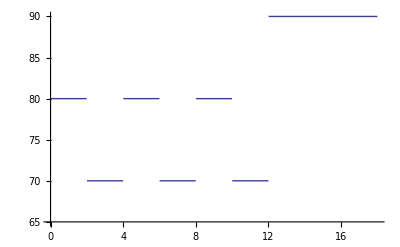

```mathematica
h[x_]=HeavisideTheta[x];
Plot[80((h[x]-h[x-2])+(h[x-4]-h[x-6])+(h[x-8]-h[x-10]))+70((h[x-2]-h[x-4])+(h[x-6]-h[x-8])+(h[x-10]-h[x-12]))+90(h[x-12]-h[x-18]),{x,-0.0001,18},PlotRange->{{-0.0001,18},{65,90}},AxesStyle->Directive[Black,30]]
```

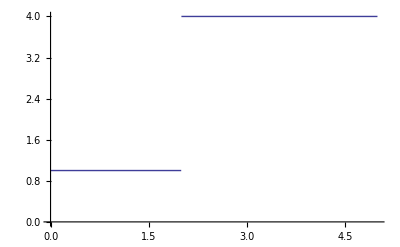

```mathematica
Plot[(h[x]-h[x-2])+4(h[x-2]-h[x-5]),{x,-0.0001,5},PlotRange->{{-0.0001,5},{0,4}},AxesStyle->Directive[Black,30]]
```

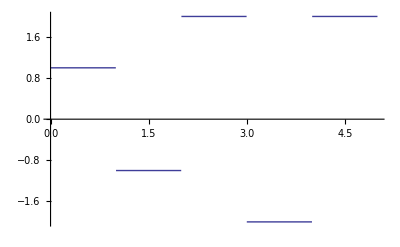

```mathematica
Plot[((h[x]-h[x-1])-(h[x-1]-h[x-2])+2(h[x-2]-h[x-3]))-2(h[x-3]-h[x-4])+2(h[x-4]-h[x-5]),{x,-0.0001,5},PlotRange->{{-0.0001,5},{-2,2}},AxesStyle->Directive[Black,30]]
```

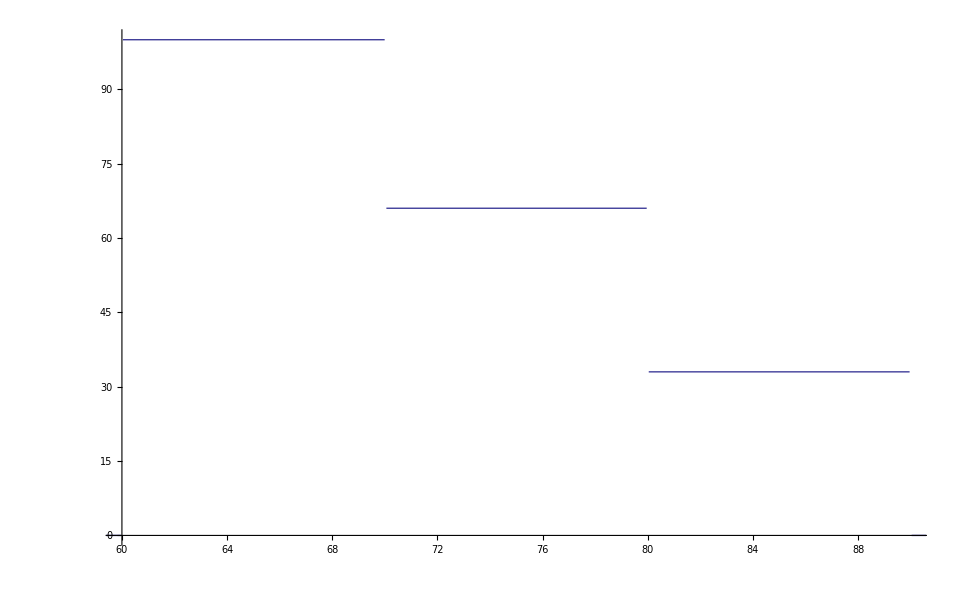

```mathematica
a=60;
Plot[100(h[x-a]-h[x-a-10])+66(h[x-a-10]-h[x-a-20])+33(h[x-a-20]-h[x-a-30]),{x,-100,100},PlotRange->{{60,90},{0,100}},AxesStyle->Directive[Black,30]]
```

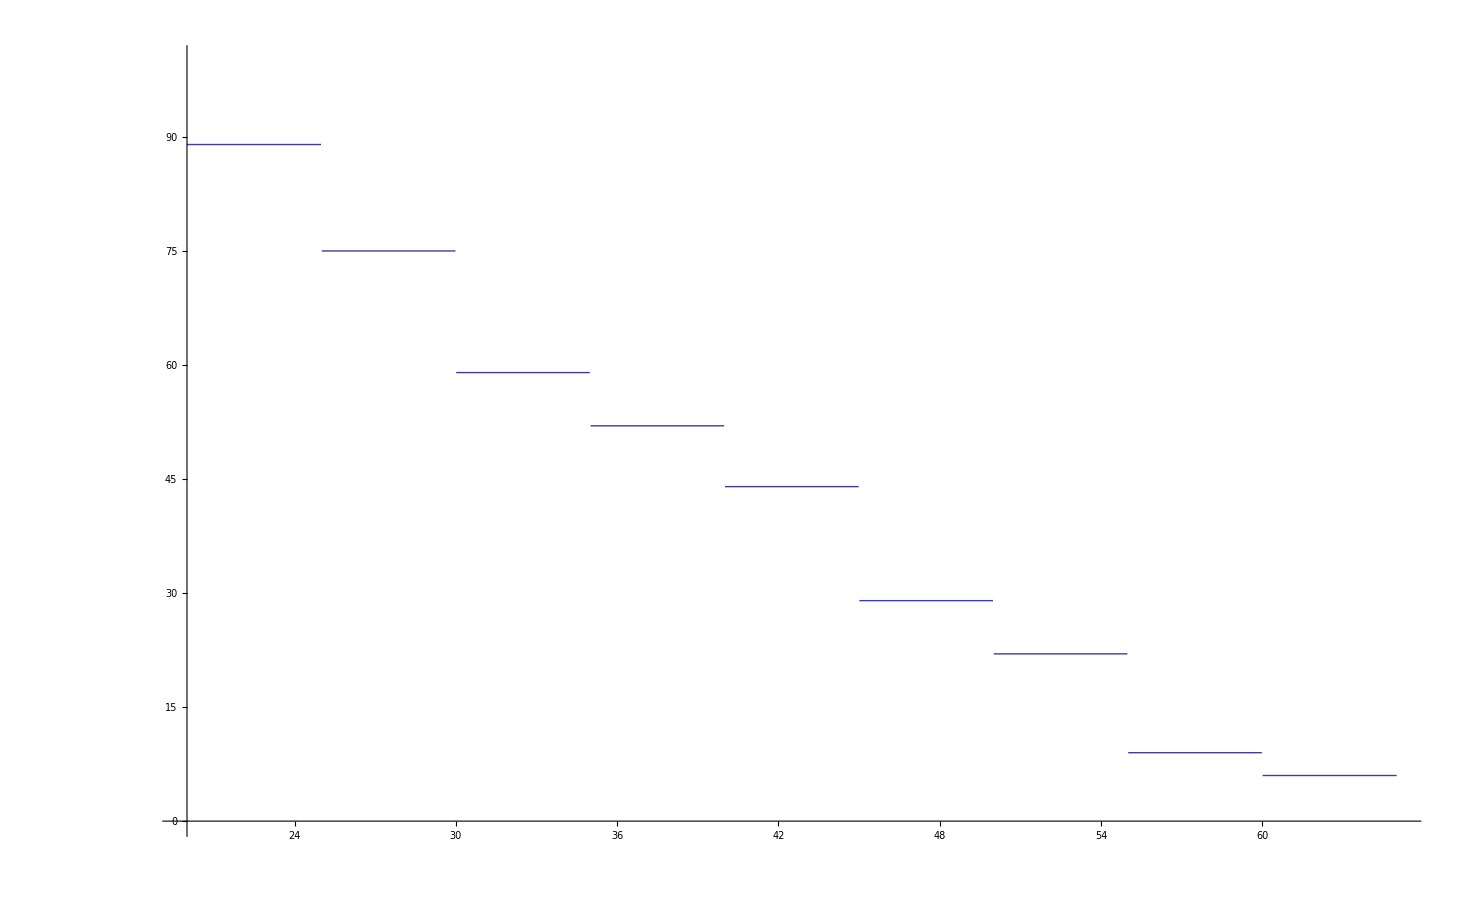

```mathematica
Esercizzio distribuzioni 2;
chi[x_,i_,f_]:=h[x-i]-h[x-f];
Plot[89chi[x,20,25]+75chi[x,25,30]+59chi[x,30,35]+52chi[x,35,40]+44chi[x,40,45]+29chi[x,45,50]+22chi[x,50,55]+9chi[x,55,60]+6chi[x,60,65],{x,20,65},PlotRange->{{20,65},{0,100}},AxesStyle->Directive[Black,30]]
```